```mathematica
r1=y^2+(x-1)^2
r2=y^2+(x+1)^2
```

(-1+x)^2+y^2

(1+x)^2+y^2

```mathematica
2r1^2-(r1^2-2)^2-(r2^2-2)^2//Simplify
```

2 ((-1+x)^2+y^2)^2-(-2+((-1+x)^2+y^2)^2)^2-(-2+((1+x)^2+y^2)^2)^2

```mathematica
R=ImplicitRegion[2 ((-1+x)^2+y^2)^2-(-2+((-1+x)^2+y^2)^2)^2-(-2+((1+x)^2+y^2)^2)^2==0,{x,y}];
```

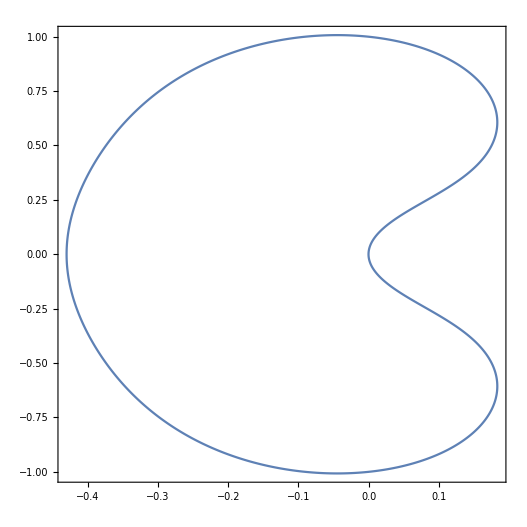

```mathematica
RegionPlot[R]
```

```mathematica
Sx[x_,y_]:=(2x)((1+x^2+y^2)/((x^2+(y+1)^2)(x^2+(y-1)^2)));
Sy[x_,y_]:=(2y)((1-x^2-y^2)/((x^2+(y+1)^2)(x^2+(y-1)^2)));
```

```mathematica
expresion[x_,y_]:=2 ((-1+x)^2+y^2)^2-(-2+((-1+x)^2+y^2)^2)^2-(-2+((1+x)^2+y^2)^2)^2
```

```mathematica
expresion[Sx[x,y],Sy[x,y]]//Simplify
```

(2 (1-2 x+x^2+y^2)^4)/((x^2+(-1+y)^2)^2 (x^2+(1+y)^2)^2)-(-2+((1-2 x+x^2+y^2)^4)/((x^2+(-1+y)^2)^2 (x^2+(1+y)^2)^2))^2-(-2+((1+2 x+x^2+y^2)^4)/((x^2+(-1+y)^2)^2 (x^2+(1+y)^2)^2))^2

```mathematica
R1=ImplicitRegion[(2 (1-2 x+x^2+y^2)^4)/((x^2+(-1+y)^2)^2 (x^2+(1+y)^2)^2)-(-2+((1-2 x+x^2+y^2)^4)/((x^2+(-1+y)^2)^2 (x^2+(1+y)^2)^2))^2-(-2+((1+2 x+x^2+y^2)^4)/((x^2+(-1+y)^2)^2 (x^2+(1+y)^2)^2))^2==0,{x,y}];
```

```mathematica
RegionPlot[R1,R]
```

RegionPlot[R1,R]

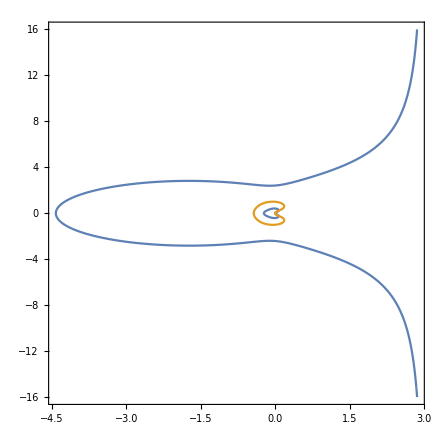

```mathematica
RegionPlot[{R1,R}]
```